# Notebook for : Gravity by Poisson & Will

Geoff Cope	
University of Utah
October 10th,2021

```mathematica
(*
I sure hope someone else does all the xAct calculations because this is downright exhausting
*)
```

## Hyperlink To Documentation

```mathematica
Hyperlink["GeneralRelativityTensors Documentation and Download",
"https://github.com/BlackHolePerturbationToolkit"]
```

[GeneralRelativityTensors Documentation and Download](https://github.com/BlackHolePerturbationToolkit)

## Hyperlink To Book And Related Papers

```mathematica
Hyperlink["Gravity by Poisson & Will ",
"https://www.cambridge.org/core/books/gravity/1F0CF38A59B1E51A63C7C3138268BE5D"]
```

[Gravity by Poisson & Will ](https://www.cambridge.org/core/books/gravity/1F0CF38A59B1E51A63C7C3138268BE5D)

## Utilities and Package Load

```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 208 Kb

{Utilities`CleanSlate`,VariationalMethods`,GeneralRelativityTensors`,GeneralRelativityTensors`CommonTensors`,GeneralRelativityTensors`TensorDerivatives`,GeneralRelativityTensors`TensorManipulation`,GeneralRelativityTensors`TensorDefinitions`,GeneralRelativityTensors`Utils`,DocumentationSearch`,ResourceLocator`,System`,Global`}

```mathematica
<<GeneralRelativityTensors`
```

```mathematica
Needs["VariationalMethods`"] (* needed for geodesic equations of metric *)
```

## Line Element and Metric Functions

```mathematica
Clear[lineToMetric]
lineToMetric[lineelement_ , differentials_]:= 
Table[If[i==j ,Coefficient[lineelement, differentials[[i]] differentials[[j]]],
(1/2)*Coefficient[lineelement, differentials[[i]] differentials[[j]]]],
{i,1,Length[differentials]},{j,1,Length[differentials]}]  ;
```

```mathematica
Clear[metricToLine]
metricToLine[metric_, differentials_]:= 
Sum[metric[[i,j]] differentials[[i]] differentials[[j]] , {i,1,Length[differentials]},{j,1,Length[differentials]}]
```

## Custom Notation

```mathematica
Clear[dtReplace]
dtReplace = {
Dt[t]-> dt , 
Dt[u]-> du , 
Dt[x]-> dx , 
 Dt[v] -> dv  
};
dtReplace // TableForm
```

Dt[t]→dt
Dt[u]→du
Dt[x]→dx
Dt[v]→dv

## Chapter 1

```mathematica
Clear[box1pt5]
box1pt5 = 
Table[ SphericalHarmonicY[i,j,θ,ϕ], {i,0,3}, {j,0,i} ]  ;
box1pt5 // MatrixForm
```

({1/(2 √π)}
{1/2 √(3/π) Cos[θ],-1/2 ⅇ^(ⅈ ϕ) √(3/(2 π)) Sin[θ]}
{1/4 √(5/π) (-1+3 Cos[θ]^2),-1/2 ⅇ^(ⅈ ϕ) √(15/(2 π)) Cos[θ] Sin[θ],1/4 ⅇ^(2 ⅈ ϕ) √(15/(2 π)) Sin[θ]^2}
{1/4 √(7/π) (-3 Cos[θ]+5 Cos[θ]^3),-1/8 ⅇ^(ⅈ ϕ) √(21/π) (-1+5 Cos[θ]^2) Sin[θ],1/4 ⅇ^(2 ⅈ ϕ) √(105/(2 π)) Cos[θ] Sin[θ]^2,-1/8 ⅇ^(3 ⅈ ϕ) √(35/π) Sin[θ]^3})

## Chapter 3

```mathematica
Clear[eq3pt1]
eq3pt1 = { 
r1[t] == (m2/m) r[t] , 
r2[t] == -(m1/m) r[t] , 
m == m1 + m2  , 
r[t] == r1[t] - r2[t] 
} ;
```

```mathematica
Clear[eq3pt5] (* Change to vector form *) 
eq3pt5 = 
L == μ h
```

L==h μ

```mathematica
Clear[eq3pt7]
eq3pt7 =  { 
n[t] == { Cos[ϕ[t]] , Sin[ϕ[t]] , 0 }   , 
λ [t]== {-Sin[ϕ[t]] , Cos[ϕ[t]] , 0 }
} ;
eq3pt7  // TableForm
```

n[t]=={Cos[ϕ[t]],Sin[ϕ[t]],0}
λ[t]=={-Sin[ϕ[t]],Cos[ϕ[t]],0}

```mathematica
D[ eq3pt7[[1]] , t ]  /. ϕ'[t]-> 1 
eq3pt7[[2]]
Thread[ ( D[ eq3pt7[[1]] , t ][[2]]  /. ϕ'[t]-> 1  ) == eq3pt7[[2]][[2]] ]
```

n'[t]=={-Sin[ϕ[t]],Cos[ϕ[t]],0}

λ[t]=={-Sin[ϕ[t]],Cos[ϕ[t]],0}

True

```mathematica
D[ eq3pt7[[2]]  , t ] 
D[ eq3pt7[[2]]  , t ]  /. ϕ'[t]-> 1 
-eq3pt7[[1]][[2]]
Thread[(  D[ eq3pt7[[2]]  , t ][[2]]  /. ϕ'[t]-> 1  ) == -eq3pt7[[1]][[2]] ]
```

λ'[t]=={-Cos[ϕ[t]] ϕ'[t],-Sin[ϕ[t]] ϕ'[t],0}

λ'[t]=={-Cos[ϕ[t]],-Sin[ϕ[t]],0}

{-Cos[ϕ[t]],-Sin[ϕ[t]],0}

True

```mathematica
n[t] /. ( eq3pt7[[1]]  /. Equal-> Rule ) 
λ[t]  /. ( eq3pt7[[2]] /. Equal-> Rule )
```

{Cos[ϕ[t]],Sin[ϕ[t]],0}

{-Sin[ϕ[t]],Cos[ϕ[t]],0}

```mathematica
Clear[eq3pt9a]
eq3pt9a = 
r[t] == 𝓇[t] * ( n[t] /. ( eq3pt7[[1]]  /. Equal-> Rule )  )
```

r[t]=={Cos[ϕ[t]] 𝓇[t],Sin[ϕ[t]] 𝓇[t],0}

```mathematica
D[ eq3pt9a  , t ]
```

r'[t]=={Cos[ϕ[t]] 𝓇'[t]-Sin[ϕ[t]] 𝓇[t] ϕ'[t],Sin[ϕ[t]] 𝓇'[t]+Cos[ϕ[t]] 𝓇[t] ϕ'[t],0}

```mathematica
Clear[eq3pt9b]
eq3pt9b = 
v[t] == 𝓇'[t] * ( n[t] /. ( eq3pt7[[1]]  /. Equal-> Rule )  )  + 𝓇[t] ϕ'[t] * (λ[t]  /. ( eq3pt7[[2]] /. Equal-> Rule )  )
```

v[t]=={Cos[ϕ[t]] 𝓇'[t]-Sin[ϕ[t]] 𝓇[t] ϕ'[t],Sin[ϕ[t]] 𝓇'[t]+Cos[ϕ[t]] 𝓇[t] ϕ'[t],0}

```mathematica
D[ eq3pt9a  , t ][[2]]
eq3pt9b[[2]]
Thread[ D[ eq3pt9a  , t ][[2]] == eq3pt9b[[2]] ]
```

{Cos[ϕ[t]] 𝓇'[t]-Sin[ϕ[t]] 𝓇[t] ϕ'[t],Sin[ϕ[t]] 𝓇'[t]+Cos[ϕ[t]] 𝓇[t] ϕ'[t],0}

{Cos[ϕ[t]] 𝓇'[t]-Sin[ϕ[t]] 𝓇[t] ϕ'[t],Sin[ϕ[t]] 𝓇'[t]+Cos[ϕ[t]] 𝓇[t] ϕ'[t],0}

True

```mathematica
Clear[eq3pt9c]
eq3pt9c =  
a[t] == ( 𝓇''[t] - 𝓇[t] ϕ'[t]^2)* ( n[t] /. ( eq3pt7[[1]]  /. Equal-> Rule )  )  + 1/𝓇[t] D[ 𝓇[t]^2 ϕ'[t] , t ] *(λ[t]  /. ( eq3pt7[[2]] /. Equal-> Rule ) )  // Expand  // Simplify
```

a[t]=={-2 Sin[ϕ[t]] 𝓇'[t] ϕ'[t]+Cos[ϕ[t]] 𝓇''[t]-𝓇[t] (Cos[ϕ[t]] ϕ'[t]^2+Sin[ϕ[t]] ϕ''[t]),2 Cos[ϕ[t]] 𝓇'[t] ϕ'[t]+Sin[ϕ[t]] 𝓇''[t]+𝓇[t] (-Sin[ϕ[t]] ϕ'[t]^2+Cos[ϕ[t]] ϕ''[t]),0}

```mathematica
D[ eq3pt9b , t ]
Thread[ D[ eq3pt9b , t ][[2]] == eq3pt9c[[2]] ]    // Expand
```

v'[t]=={-2 Sin[ϕ[t]] 𝓇'[t] ϕ'[t]-Cos[ϕ[t]] 𝓇[t] ϕ'[t]^2+Cos[ϕ[t]] 𝓇''[t]-Sin[ϕ[t]] 𝓇[t] ϕ''[t],2 Cos[ϕ[t]] 𝓇'[t] ϕ'[t]-Sin[ϕ[t]] 𝓇[t] ϕ'[t]^2+Sin[ϕ[t]] 𝓇''[t]+Cos[ϕ[t]] 𝓇[t] ϕ''[t],0}

{True,True,True}

```mathematica
Clear[eq3pt10]
eq3pt10 = 
𝓇[t]^2 ϕ'[t] == h
```

𝓇[t]^2 ϕ'[t]==h

```mathematica
Flatten[Solve[ eq3pt10  , ϕ'[t]]][[1]]
```

ϕ'[t]→h/𝓇[t]^2

```mathematica
( 𝓇''[t] - 𝓇[t] ϕ'[t]^2)
( 𝓇''[t] - 𝓇[t] ϕ'[t]^2) /. Flatten[Solve[ eq3pt10  , ϕ'[t]]][[1]] 

Clear[eq3pt11]
eq3pt11 = 
( ( 𝓇''[t] - 𝓇[t] ϕ'[t]^2) /. Flatten[Solve[ eq3pt10  , ϕ'[t]]][[1]]  )  == -((G m)/𝓇[t]^2)
```

-𝓇[t] ϕ'[t]^2+𝓇''[t]

-h^2/𝓇[t]^3+𝓇''[t]

-h^2/𝓇[t]^3+𝓇''[t]==-(G m)/𝓇[t]^2

```mathematica
Clear[eq3pt12a]
eq3pt12a = 
Expand[ MultiplySides[eq3pt11 , 𝓇'[t],Assumptions->  𝓇'[t]!= 0  ] ]
```

-(h^2 𝓇'[t])/𝓇[t]^3+𝓇'[t] 𝓇''[t]==-(G m 𝓇'[t])/𝓇[t]^2

```mathematica
Integrate[ eq3pt12a[[1]][[1]] , t ] 
Integrate[ eq3pt12a[[1]][[2]] , t ] 
Integrate[ eq3pt12a[[2]] , t ]
```

h^2/(2 𝓇[t]^2)

1/2 𝓇'[t]^2

(G m)/𝓇[t]

```mathematica
Clear[eq3pt12]
eq3pt12 = 
Integrate[ eq3pt12a[[1]][[1]] , t ]  + Integrate[ eq3pt12a[[1]][[2]] , t ]  - Integrate[ eq3pt12a[[2]] , t ]  == ε
```

h^2/(2 𝓇[t]^2)-(G m)/𝓇[t]+1/2 𝓇'[t]^2==ε

```mathematica
Clear[eq3pt14] (* redefine the argument of Veff *) 
eq3pt14 = 
Veff[𝓇[t]]   ==  eq3pt12[[1]][[1;;2]]
```

Veff[𝓇[t]]==h^2/(2 𝓇[t]^2)-(G m)/𝓇[t]

```mathematica
( eq3pt14 /. Equal-> Rule  )
```

Veff[𝓇[t]]→h^2/(2 𝓇[t]^2)-(G m)/𝓇[t]

```mathematica
Clear[eq3pt13] (* or just leave as Veff *) 
eq3pt13 = 
eq3pt12[[1]][[3]] == ε - ( Veff[𝓇[t]]  /. ( eq3pt14 /. Equal-> Rule  )  )
```

1/2 𝓇'[t]^2==ε-h^2/(2 𝓇[t]^2)+(G m)/𝓇[t]

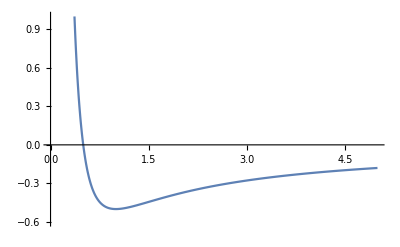

```mathematica
Plot[ Evaluate[(eq3pt14[[2]]  /. 𝓇[t]-> 𝓇  /. G-> 1 /. m-> 1 /. h-> 1 )] , {𝓇,0,5}, PlotRange-> {-0.6 , 1 }  ]
```

```mathematica
(* Try and remember how to do this chain rule *) 
Clear[eq3pt17a]
eq3pt17a = 
 𝓇[t] == 1/u[t]

eq3pt11
```

𝓇[t]==1/u[t]

-h^2/𝓇[t]^3+𝓇''[t]==-(G m)/𝓇[t]^2

```mathematica
D[ eq3pt17a  , t ]
```

𝓇'[t]==-u'[t]/u[t]^2

```mathematica
D[ eq3pt17a, t ]
```

u'[t]==-𝓇'[t]/𝓇[t]^2

```mathematica
Clear[eq3pt17]
eq3pt17 = 
u''[t] + u[t]== (G m)/h^2
```

u[t]+u''[t]==(G m)/h^2

```mathematica
(* Too lazy to do the phase shift *) 
Flatten[DSolve[ eq3pt17  , u[t]  , t ] ][[1]]
```

u[t]→(G m)/h^2+C[1] Cos[t]+C[2] Sin[t]

```mathematica
Clear[eq3pt18]
eq3pt18 = 
u[t] == (G m)/h^2 ( 1 + ℯ Cos[ϕ[t]-ω] )
```

u[t]==(G m (1+ℯ Cos[ω-ϕ[t]]))/h^2

```mathematica
Clear[eq3pt20]
eq3pt20 = 
p == h^2/(G m)
```

p==h^2/(G m)

```mathematica
Flatten[Solve[ eq3pt20 , G ] ][[1]]
```

G→h^2/(m p)

```mathematica
eq3pt17a  /. ( eq3pt18  /. Equal-> Rule )
```

𝓇[t]==h^2/(G m (1+ℯ Cos[ω-ϕ[t]]))

```mathematica
Clear[eq3pt19]
eq3pt19 = 
eq3pt17a  /. ( eq3pt18  /. Equal-> Rule )   /. Flatten[Solve[ eq3pt20 , G ] ][[1]]
```

𝓇[t]==p/(1+ℯ Cos[ω-ϕ[t]])

```mathematica
Clear[eq3pt21]
eq3pt21 = {
Subscript[r, peri] == p/(1+ℯ), 
Subscript[r, apo] == p/(1-ℯ)
} ;
eq3pt21  // TableForm
```

r_peri==p/(1+ℯ)
r_apo==p/(1-ℯ)

```mathematica
Flatten[Solve[ eq3pt21  , {p,ℯ} ]] // TableForm
```

p→(2 r_apo r_peri)/(r_apo+r_peri)
ℯ→-(-r_apo+r_peri)/(r_apo+r_peri)

```mathematica
Clear[eq3pt22]
eq3pt22 = 
a ==( (  1/2( Subscript[r, peri] + Subscript[r, apo] ) /. (eq3pt21   /. Equal-> Rule ) )  // Expand  // Simplify  )
```

a==p/(1-ℯ^2)

```mathematica
Flatten[Solve[ eq3pt22  , p ]][[1]]
```

p→-a (-1+ℯ^2)

```mathematica
eq3pt10
( eq3pt19 /. Equal-> Rule )  
Flatten[Solve[eq3pt20 ,h]][[2]]
```

𝓇[t]^2 ϕ'[t]==h

𝓇[t]→p/(1+ℯ Cos[ω-ϕ[t]])

h→√G √m √p

```mathematica
Flatten[Solve[ eq3pt10 , ϕ'[t]]][[1]] 
Flatten[Solve[ eq3pt10 , ϕ'[t]]][[1]]  /. ( eq3pt19 /. Equal-> Rule  ) 

Clear[eq3pt25b]
eq3pt25b = 
( Flatten[Solve[ eq3pt10 , ϕ'[t]]][[1]]  /. ( eq3pt19 /. Equal-> Rule  )  /. (Flatten[Solve[eq3pt20 ,h]][[2]] ) )  /. Rule-> Equal
```

ϕ'[t]→h/𝓇[t]^2

ϕ'[t]→(h (1+ℯ Cos[ω-ϕ[t]])^2)/p^2

ϕ'[t]==(√G √m (1+ℯ Cos[ω-ϕ[t]])^2)/p^(3/2)

```mathematica
D[ eq3pt19 , t ] 

Clear[eq3pt25a]
eq3pt25a= 
D[ eq3pt19 , t ]  /. (eq3pt25b  /. Equal-> Rule )
```

𝓇'[t]==-(p ℯ Sin[ω-ϕ[t]] ϕ'[t])/(1+ℯ Cos[ω-ϕ[t]])^2

𝓇'[t]==-(√G √m ℯ Sin[ω-ϕ[t]])/(√p)

```mathematica
𝓇'[t]^2+ 𝓇[t]^2 ϕ'[t]^2
```

𝓇'[t]^2+𝓇[t]^2 ϕ'[t]^2

```mathematica
( eq3pt19 /. Equal-> Rule )  
( eq3pt25a /. Equal-> Rule )
( eq3pt25b /. Equal-> Rule )
```

𝓇[t]→p/(1+ℯ Cos[ω-ϕ[t]])

𝓇'[t]→-(√G √m ℯ Sin[ω-ϕ[t]])/(√p)

ϕ'[t]→(√G √m (1+ℯ Cos[ω-ϕ[t]])^2)/p^(3/2)

```mathematica
( 𝓇'[t]^2+ 𝓇[t]^2 ϕ'[t]^2 ) /. ( eq3pt25a /. Equal-> Rule ) /. ( eq3pt25b /. Equal-> Rule )   /. ( eq3pt19 /. Equal-> Rule )
```

(G m (1+ℯ Cos[ω-ϕ[t]])^2)/p+(G m ℯ^2 Sin[ω-ϕ[t]]^2)/p

```mathematica
Clear[eq3pt26a]
eq3pt26a = 
v^2== ( ( 𝓇'[t]^2+ 𝓇[t]^2 ϕ'[t]^2 ) /. ( eq3pt25a /. Equal-> Rule ) /. ( eq3pt25b /. Equal-> Rule )   /. ( eq3pt19 /. Equal-> Rule )  )   //   TrigExpand  // FullSimplify
```

v^2==(G m (1+ℯ^2+2 ℯ Cos[ω-ϕ[t]]))/p

```mathematica
( Flatten[Solve[ ( eq3pt19  /. ( Cos[ω-ϕ[t]]-> β )  ), β ]][[1]]  /. β-> Cos[ω-ϕ[t]] )
```

Cos[ω-ϕ[t]]→(p-𝓇[t])/(ℯ 𝓇[t])

```mathematica
Clear[eq3pt26b]
eq3pt26b = 
v^2== Collect[ ( eq3pt26a  /. ( Flatten[Solve[ ( eq3pt19  /. ( Cos[ω-ϕ[t]]-> β )  ), β ]][[1]]  /. β-> Cos[ω-ϕ[t]] )  // Expand  ) , G m ]
```

v^2==G m (-1/p+ℯ^2/p+2/𝓇[t])

```mathematica
Clear[eq3pt26]
eq3pt26 =  { 
eq3pt26a  , 
eq3pt26b 
} ;
eq3pt26  // TableForm
```

v^2==(G m (1+ℯ^2+2 ℯ Cos[ω-ϕ[t]]))/p
v^2==G m (-1/p+ℯ^2/p+2/𝓇[t])

```mathematica
eq3pt26[[2]]
eq3pt26[[2]][[2]]
Sqrt[ eq3pt26[[2]][[2]] ] 
eq3pt12
```

v^2==G m (-1/p+ℯ^2/p+2/𝓇[t])

G m (-1/p+ℯ^2/p+2/𝓇[t])

√(G m (-1/p+ℯ^2/p+2/𝓇[t]))

```mathematica
(* remember, on the lhs of 3.22 you have kinetic minus potential *) 
Flatten[Solve[eq3pt20, h ]][[2]] 
Flatten[Solve[ eq3pt22, p ]][[1]] 
eq3pt12
eq3pt12[[1]]
eq3pt26[[2]]
eq3pt26[[2]][[2]]
```

h→√G √m √p

p→-a (-1+ℯ^2)

h^2/(2 𝓇[t]^2)-(G m)/𝓇[t]+1/2 𝓇'[t]^2==ε

h^2/(2 𝓇[t]^2)-(G m)/𝓇[t]+1/2 𝓇'[t]^2

v^2==G m (-1/p+ℯ^2/p+2/𝓇[t])

G m (-1/p+ℯ^2/p+2/𝓇[t])

```mathematica
Clear[eq3pt27a]
eq3pt27a = 
μ ( ( 1/2 eq3pt26[[2]][[2]] -(G m)/𝓇[t]  ) // Expand  // Simplify  )
```

(G m (-1+ℯ^2) μ)/(2 p)

```mathematica
Clear[eq3pt27b]
eq3pt27b =
eq3pt27a /. Flatten[Solve[ eq3pt22, p ]][[1]]
```

-(G m μ)/(2 a)

```mathematica
eq3pt5
Flatten[Solve[eq3pt20, h ]][[2]] 

Clear[eq3pt28] (* Change to vector *) 
eq3pt28 = eq3pt5 /. Flatten[Solve[eq3pt20, h ]][[2]]
```

L==h μ

h→√G √m √p

L==√G √m √p μ

```mathematica
eq3pt25b
eq3pt25b /. ϕ'[t] -> (dϕ/dt) 

Clear[eq3pt29a]
eq3pt29a = 
( Flatten[Solve[ ( eq3pt25b /. ϕ'[t] -> (dϕ/dt)  ) , dt ] ][[1]]  ) /.Rule-> Equal
```

ϕ'[t]==(√G √m (1+ℯ Cos[ω-ϕ[t]])^2)/p^(3/2)

dϕ/dt==(√G √m (1+ℯ Cos[ω-ϕ[t]])^2)/p^(3/2)

dt==(dϕ p^(3/2))/(√G √m (1+ℯ Cos[ω-ϕ[t]])^2)

```mathematica
eq3pt29a[[1]] (* Integrate this *) 
Coefficient[ ( eq3pt29a[[2]] /. ϕ[t]-> φ[t] )  , dϕ ] (* Integrate this *)
```

dt

p^(3/2)/(√G √m (1+ℯ Cos[ω-φ[t]])^2)

```mathematica
Clear[eq3pt29] (* get rid of time dependence in trig functions? This doesn't work, change this *) 
eq3pt29 = 
t- T == Inactive[ Integrate[ Coefficient[ ( eq3pt29a[[2]] /. ϕ[t]-> φ[t] )  , dϕ ] , {φ[t], ω,ϕ[t] } ] ]
```

t-T==Inactive[∫_ω^ϕ[t] Coefficient[eq3pt29a⟦2⟧/.ϕ[t]→φ[t],dϕ]ⅆφ[t]]

```mathematica
Clear[eq3pt30]
eq3pt30 = {
Cos[f] == (Cos[u]-ℯ)/(1 - ℯ Cos[u]) , 
Sin[f] == (√(1-ℯ^2)Sin[u])/(1 - ℯ Cos[u]) , 
f == ϕ- ω (* Make f and ϕ time dependent or leave? remember ω is constant of integration?  *) 
} ;
eq3pt30  // TableForm
```

Cos[f]==(-ℯ+Cos[u])/(1-ℯ Cos[u])
Sin[f]==(√(1-ℯ^2) Sin[u])/(1-ℯ Cos[u])
f==ϕ-ω

```mathematica
eq3pt30 /. Sin[u]-> α  /. Cos[u]-> β

Clear[eq3pt31]
eq3pt31 = 
( ( Flatten[Solve[ ( eq3pt30 /. Sin[u]-> α  /. Cos[u]-> β ) , {α,β} ]]  /. { α-> Sin[u] , β-> Cos[u] }  )  // Expand  // Simplify  ) /. Rule-> Equal
```

{Cos[f]==(-ℯ+β)/(1-ℯ β),Sin[f]==(√(1-ℯ^2) α)/(1-ℯ β)}

{Sin[u]==(√(1-ℯ^2) Sin[f])/(1+ℯ Cos[f]),Cos[u]==(ℯ+Cos[f])/(1+ℯ Cos[f])}

```mathematica
eq3pt30[[2]]
eq3pt30[[1]]

Numerator[ eq3pt30[[2]][[2]] ] 
Denominator[ eq3pt30[[2]][[2]] ] 
Numerator[ eq3pt30[[1]][[2]] ]
```

Sin[f]==(√(1-ℯ^2) Sin[u])/(1-ℯ Cos[u])

Cos[f]==(-ℯ+Cos[u])/(1-ℯ Cos[u])

√(1-ℯ^2) Sin[u]

1-ℯ Cos[u]

-ℯ+Cos[u]

```mathematica
Clear[eq3pt31a] (* Try to verify this later *) 
eq3pt31a = {
opp == Numerator[ eq3pt30[[2]][[2]] ]  , 
adj == Numerator[ eq3pt30[[1]][[2]] ]   , 
hyp == Denominator[ eq3pt30[[2]][[2]] ] 
}  /. Equal-> Rule ;
eq3pt31a  // TableForm
```

opp→√(1-ℯ^2) Sin[u]
adj→-ℯ+Cos[u]
hyp→1-ℯ Cos[u]

```mathematica
Clear[eq3pt32]
eq3pt32 =  { 
Tan[f/2] == √((1+ℯ)/(1-ℯ)) Tan[u/2] , 
Tan[f[u]/2] == √((1+ℯ)/(1-ℯ)) Tan[u/2] , 
Tan[u/2] == √((1+ℯ)/(1-ℯ)) Tan[u[f]/2]
} ;
eq3pt32  // TableForm
```

Tan[f/2]==√((1+ℯ)/(1-ℯ)) Tan[u/2]
Tan[f[u]/2]==√((1+ℯ)/(1-ℯ)) Tan[u/2]
Tan[u/2]==√((1+ℯ)/(1-ℯ)) Tan[u[f]/2]

```mathematica
(* Too tired to change the variables to do the appropriate differentiation *) 
D[ eq3pt32[[2]] , u ] 
Flatten[Solve[ D[ eq3pt32[[2]] , u ]  , f'[u] ] ][[1]]
```

1/2 Sec[f[u]/2]^2 f'[u]==1/2 √((1+ℯ)/(1-ℯ)) Sec[u/2]^2

f'[u]→√((-1-ℯ)/(-1+ℯ)) Cos[f[u]/2]^2 Sec[u/2]^2

## Box 3.2 Page 153 Needed Before Equations 3.40

```mathematica
(* Poisson and Will Gravity page 153 *)
Clear[R1]
R1=
({{Cos[ω], -Sin[ω], 0}, {Sin[ω], Cos[ω], 0}, {0, 0, 1}});

Clear[R2]
R2 = 
({{1, 0, 0}, {0, Cos[ι], -Sin[ι]}, {0, Sin[ι], Cos[ι]}});

Clear[R3]
R3 = 
({{Cos[Ω], -Sin[Ω], 0}, {Sin[Ω], Cos[Ω], 0}, {0, 0, 1}});

Clear[𝓍]
𝓍 = { x ,  y , z }  ;

Clear[𝒳]
𝒳 = { X , Y , Z }  ;
```

```mathematica
R3 . R2 . R1 . 𝓍  // Expand // Simplify  // MatrixForm
```

(-y Cos[Ω] Sin[ω]+(z Sin[ι]-x Cos[ι] Sin[ω]) Sin[Ω]+Cos[ω] (x Cos[Ω]-y Cos[ι] Sin[Ω])
-z Cos[Ω] Sin[ι]+Cos[ι] Cos[Ω] (y Cos[ω]+x Sin[ω])+(x Cos[ω]-y Sin[ω]) Sin[Ω]
z Cos[ι]+Sin[ι] (y Cos[ω]+x Sin[ω]))

```mathematica
Clear[box3pt2a]
box3pt2a = { 
Collect[ Thread[ 𝒳 == (  R3 . R2 . R1 . 𝓍  // Expand // Simplify ) ][[1]]  , {x,y,z} ]  , 
Collect[ Thread[ 𝒳 == (  R3 . R2 . R1 . 𝓍  // Expand // Simplify ) ][[2]] , {x,y,z} ]  , 
Collect[ Thread[ 𝒳 == (  R3 . R2 . R1 . 𝓍  // Expand // Simplify ) ][[3]] ,{x,y,z} ] 
} ;
box3pt2a // TableForm
```

X==z Sin[ι] Sin[Ω]+y (-Cos[Ω] Sin[ω]-Cos[ι] Cos[ω] Sin[Ω])+x (Cos[ω] Cos[Ω]-Cos[ι] Sin[ω] Sin[Ω])
Y==-z Cos[Ω] Sin[ι]+x (Cos[ι] Cos[Ω] Sin[ω]+Cos[ω] Sin[Ω])+y (Cos[ι] Cos[ω] Cos[Ω]-Sin[ω] Sin[Ω])
Z==z Cos[ι]+y Cos[ω] Sin[ι]+x Sin[ι] Sin[ω]

```mathematica
Clear[box3pt2b]
box3pt2b= { 
x == r Cos[f] , 
y == r Sin[f] , 
z == 0
}  ;
box3pt2b /. Equal-> Rule  // TableForm
```

x→r Cos[f]
y→r Sin[f]
z→0

```mathematica
Clear[box3pt2d] (* set these equal to basis vectors if needed and figure out why transpose  *) 
box3pt2d  = 
Transpose[Table[{ Coefficient[ box3pt2a[[i]][[2]], x ] ,Coefficient[ box3pt2a[[i]][[2]], y ] , Coefficient[ box3pt2a[[i]][[2]], z ]  } , {i,1,3}]]   ;
box3pt2d // MatrixForm
```

(Cos[ω] Cos[Ω]-Cos[ι] Sin[ω] Sin[Ω] | Cos[ι] Cos[Ω] Sin[ω]+Cos[ω] Sin[Ω] | Sin[ι] Sin[ω]
-Cos[Ω] Sin[ω]-Cos[ι] Cos[ω] Sin[Ω] | Cos[ι] Cos[ω] Cos[Ω]-Sin[ω] Sin[Ω] | Cos[ω] Sin[ι]
Sin[ι] Sin[Ω] | -Cos[Ω] Sin[ι] | Cos[ι])

```mathematica
box3pt2d [[1,1;;3]] /. ω-> ω+f (* needed for equation 3.42 *) 
box3pt2d [[2,1;;3]]  /. ω-> ω+f (* needed for equation 3.43 *)
```

{Cos[f+ω] Cos[Ω]-Cos[ι] Sin[f+ω] Sin[Ω],Cos[ι] Cos[Ω] Sin[f+ω]+Cos[f+ω] Sin[Ω],Sin[ι] Sin[f+ω]}

{-Cos[Ω] Sin[f+ω]-Cos[ι] Cos[f+ω] Sin[Ω],Cos[ι] Cos[f+ω] Cos[Ω]-Sin[f+ω] Sin[Ω],Cos[f+ω] Sin[ι]}

```mathematica
Clear[eq3pt40]
eq3pt40 = 
Flatten[Solve[ ( box3pt2a /. ( box3pt2b /. Equal-> Rule  ) ) , {X,Y,Z} ]] // Expand // FullSimplify   ;
eq3pt40// TableForm
```

X→r (Cos[f+ω] Cos[Ω]-Cos[ι] Sin[f+ω] Sin[Ω])
Y→r (Cos[ι] Cos[Ω] Sin[f+ω]+Cos[f+ω] Sin[Ω])
Z→r Sin[ι] Sin[f+ω]

```mathematica
Clear[eq3pt40a]
eq3pt40a = 
eq3pt40[[1]]
```

X→r (Cos[f+ω] Cos[Ω]-Cos[ι] Sin[f+ω] Sin[Ω])

```mathematica
Clear[eq3pt40b]
eq3pt40b = 
eq3pt40[[2]]
```

Y→r (Cos[ι] Cos[Ω] Sin[f+ω]+Cos[f+ω] Sin[Ω])

```mathematica
Clear[eq3pt40c]
eq3pt40c = 
eq3pt40[[3]]
```

Z→r Sin[ι] Sin[f+ω]

```mathematica
Clear[eq3pt40d] (* Not numbered *) 
eq3pt40d = 
𝓇[t] == p/(1+ ℯ Cos[f[t]])  /. Equal-> Rule
```

𝓇[t]→p/(1+ℯ Cos[f[t]])

```mathematica
eq3pt30[[3]]  (* Make time dependent? *) 
eq3pt40d 
( ( eq3pt25a  /. Equal-> Rule  )  /.  ϕ[t]-> ( ω-f[t] ) )  
eq3pt40a[[2]] /. r-> 𝓇[t] /. f-> f[t] 
D[ ( eq3pt40a[[2]] /. r-> 𝓇[t] /. f-> f[t]  ) , t ]
```

f==ϕ-ω

𝓇[t]→p/(1+ℯ Cos[f[t]])

𝓇'[t]→-(√G √m ℯ Sin[f[t]])/(√p)

(Cos[Ω] Cos[ω+f[t]]-Cos[ι] Sin[Ω] Sin[ω+f[t]]) 𝓇[t]

𝓇[t] (-Cos[ι] Cos[ω+f[t]] Sin[Ω] f'[t]-Cos[Ω] Sin[ω+f[t]] f'[t])+(Cos[Ω] Cos[ω+f[t]]-Cos[ι] Sin[Ω] Sin[ω+f[t]]) 𝓇'[t]

```mathematica
D[ ( eq3pt40a[[2]] /. r-> 𝓇[t] /. f-> f[t]  ) , t ]  /. eq3pt40d
```

(p (-Cos[ι] Cos[ω+f[t]] Sin[Ω] f'[t]-Cos[Ω] Sin[ω+f[t]] f'[t]))/(1+ℯ Cos[f[t]])+(Cos[Ω] Cos[ω+f[t]]-Cos[ι] Sin[Ω] Sin[ω+f[t]]) 𝓇'[t]

```mathematica
Clear[eq3pt41a] (* No idea if this is right, but looks close *) 
eq3pt41a = 
( D[ ( eq3pt40a[[2]] /. r-> 𝓇[t] /. f-> f[t]  ) , t ]  /. eq3pt40d  ) /.( ( eq3pt25a  /. Equal-> Rule  )  /.  ϕ[t]-> ( ω-f[t] ) )   /. f'[t]-> 0  // FullSimplify
```

(√G √m ℯ Sin[f[t]] (-Cos[Ω] Cos[ω+f[t]]+Cos[ι] Sin[Ω] Sin[ω+f[t]]))/(√p)

```mathematica
Clear[eq3pt41b]
eq3pt41b = 
D[ ( eq3pt40b[[2]]/. r-> 𝓇[t] /. f-> f[t]  ) , t ]  /. f'[t]-> 0  /. ( ( eq3pt25a  /. Equal-> Rule  )  /.  ϕ[t]-> ( ω-f[t] ) )
```

-(√G √m ℯ Sin[f[t]] (Cos[ω+f[t]] Sin[Ω]+Cos[ι] Cos[Ω] Sin[ω+f[t]]))/(√p)

```mathematica
eq3pt40c[[2]] /. r-> 𝓇[t] /. f-> f[t]
D[ ( eq3pt40c[[2]] /. r-> 𝓇[t] /. f-> f[t] ) , t ]  /. f'[t]-> 0
```

```mathematica
Clear[eq3pt41c]
eq3pt41c = 
D[ ( eq3pt40c[[2]] /. r-> 𝓇[t] /. f-> f[t] ) , t ]  /. f'[t]-> 0  /. ( ( eq3pt25a  /. Equal-> Rule  )  /.  ϕ[t]-> ( ω-f[t] ) )
```

-(√G √m ℯ Sin[ι] Sin[f[t]] Sin[ω+f[t]])/(√p)

```mathematica
box3pt2d[[1,1;;3]] /. ω-> ω+f
```

{Cos[f+ω] Cos[Ω]-Cos[ι] Sin[f+ω] Sin[Ω],-Cos[Ω] Sin[f+ω]-Cos[ι] Cos[f+ω] Sin[Ω],Sin[ι] Sin[Ω]}

```mathematica
Clear[eq3pt42] (* Do dot product with {eX,eY,eZ}  or leave implied? *) 
eq3pt42 = 
n == box3pt2d [[1,1;;3]] /. ω-> ω+f
```

n=={Cos[f+ω] Cos[Ω]-Cos[ι] Sin[f+ω] Sin[Ω],Cos[ι] Cos[Ω] Sin[f+ω]+Cos[f+ω] Sin[Ω],Sin[ι] Sin[f+ω]}

```mathematica
Clear[eq3pt43](* Do dot product with {eX,eY,eZ}  or leave implied? *)  
eq3pt43 = 
λ == box3pt2d [[2,1;;3]]  /. ω-> ω+f
```

λ=={-Cos[Ω] Sin[f+ω]-Cos[ι] Cos[f+ω] Sin[Ω],Cos[ι] Cos[f+ω] Cos[Ω]-Sin[f+ω] Sin[Ω],Cos[f+ω] Sin[ι]}

```mathematica
Clear[eq3pt44](* Do dot product with {eX,eY,eZ}  or leave implied? *)   
eq3pt44 = 
Subscript[e, x]== box3pt2d [[1,1;;3]]
```

e_x=={Cos[ω] Cos[Ω]-Cos[ι] Sin[ω] Sin[Ω],Cos[ι] Cos[Ω] Sin[ω]+Cos[ω] Sin[Ω],Sin[ι] Sin[ω]}

```mathematica
Clear[eq3pt45](* Do dot product with {eX,eY,eZ}  or leave implied? *)   
eq3pt45 = 
Subscript[e, z]== box3pt2d [[3,1;;3]]
```

e_z=={Sin[ι] Sin[Ω],-Cos[Ω] Sin[ι],Cos[ι]}

```mathematica
Clear[eq3pt107]
eq3pt107 = 
n1 == { Cos[Ω1 t] , Sin[Ω1 t], 0} /. Equal-> Rule
```

n1→{Cos[t Ω1],Sin[t Ω1],0}

```mathematica
Clear[eq3pt108]
eq3pt108 = 
n2 == { Cos[Ω2 t+ψ] , Sin[Ω2 t+ψ], 0} /. Equal-> Rule
```

n2→{Cos[ψ+t Ω2],Sin[ψ+t Ω2],0}

```mathematica
Clear[eq3pt109]
eq3pt109 = 
e == { Sin[α] Cos[β] , Sin[α] Sin[β] , Cos[α] }  /. Equal-> Rule
```

e→{Cos[β] Sin[α],Sin[α] Sin[β],Cos[α]}

```mathematica
Clear[eq3pt106]
eq3pt106 = 
(* consant in front *) ( (m1/r1^3)( e  . n1 ) Cross[e,n1] +(m2/r2^3)  ( e  . n2 ) Cross[e,n2] /. eq3pt109 /. eq3pt108 /. eq3pt107 ) // Expand // Simplify
```

{{(Sin[2 α] (-((m2 r1^3+m1 r2^3) Sin[β])+m1 r2^3 Sin[β-2 t Ω1]+m2 r1^3 Sin[β-2 (ψ+t Ω2)]))/(4 r1^3 r2^3),(Sin[2 α] (m1 r2^3 Cos[β]+m1 r2^3 Cos[β-2 t Ω1]+m2 r1^3 (-Sin[β]+Sin[β-2 (ψ+t Ω2)])))/(4 r1^3 r2^3),-(Sin[α] (-m1 r2^3 Cos[α+2 β-2 t Ω1]+m1 r2^3 Cos[α-2 β+2 t Ω1]+4 m2 r1^3 Cos[α] Cos[β-ψ-t Ω2] Sin[ψ+t Ω2]))/(4 r1^3 r2^3)},{(Sin[2 α] (m2 r1^3 Cos[β]+m2 r1^3 Cos[β-2 (ψ+t Ω2)]-2 m1 r2^3 Cos[β-t Ω1] Sin[t Ω1]))/(4 r1^3 r2^3),(((m2 r1^3+m1 r2^3) Cos[β]+m1 r2^3 Cos[β-2 t Ω1]+m2 r1^3 Cos[β-2 (ψ+t Ω2)]) Sin[2 α])/(4 r1^3 r2^3),((m2 r1^3 Cos[α-β]+m2 r1^3 Cos[α+β]+m1 r2^3 Cos[α+2 β-2 t Ω1]-m1 r2^3 Cos[α-2 β+2 t Ω1]+m2 r1^3 Cos[α-β+2 ψ+2 t Ω2]+m2 r1^3 Cos[α+β-2 (ψ+t Ω2)]) Sin[α])/(4 r1^3 r2^3)},{(Sin[α] (m2 r1^3 Cos[α+2 β-2 ψ-2 t Ω2]-m2 r1^3 Cos[α+2 (-β+ψ+t Ω2)]-4 m1 r2^3 Cos[α] Cos[β-t Ω1] Sin[t Ω1]))/(4 r1^3 r2^3),((m1 r2^3 Cos[α-β]+m1 r2^3 Cos[α+β]+m1 r2^3 Cos[α+β-2 t Ω1]+m1 r2^3 Cos[α-β+2 t Ω1]+m2 r1^3 Cos[α+2 β-2 ψ-2 t Ω2]-m2 r1^3 Cos[α-2 β+2 ψ+2 t Ω2]) Sin[α])/(4 r1^3 r2^3),-(Sin[α]^2 (m1 r2^3 Sin[2 (β-t Ω1)]+m2 r1^3 Sin[2 β-2 ψ-2 t Ω2]))/(2 r1^3 r2^3)}}

```mathematica
eq3pt106[[1]]
```

{(Sin[2 α] (-((m2 r1^3+m1 r2^3) Sin[β])+m1 r2^3 Sin[β-2 t Ω1]+m2 r1^3 Sin[β-2 (ψ+t Ω2)]))/(4 r1^3 r2^3),(Sin[2 α] (m1 r2^3 Cos[β]+m1 r2^3 Cos[β-2 t Ω1]+m2 r1^3 (-Sin[β]+Sin[β-2 (ψ+t Ω2)])))/(4 r1^3 r2^3),-(Sin[α] (-m1 r2^3 Cos[α+2 β-2 t Ω1]+m1 r2^3 Cos[α-2 β+2 t Ω1]+4 m2 r1^3 Cos[α] Cos[β-ψ-t Ω2] Sin[ψ+t Ω2]))/(4 r1^3 r2^3)}

```mathematica
eq3pt106[[2]]
```

{(Sin[2 α] (m2 r1^3 Cos[β]+m2 r1^3 Cos[β-2 (ψ+t Ω2)]-2 m1 r2^3 Cos[β-t Ω1] Sin[t Ω1]))/(4 r1^3 r2^3),(((m2 r1^3+m1 r2^3) Cos[β]+m1 r2^3 Cos[β-2 t Ω1]+m2 r1^3 Cos[β-2 (ψ+t Ω2)]) Sin[2 α])/(4 r1^3 r2^3),((m2 r1^3 Cos[α-β]+m2 r1^3 Cos[α+β]+m1 r2^3 Cos[α+2 β-2 t Ω1]-m1 r2^3 Cos[α-2 β+2 t Ω1]+m2 r1^3 Cos[α-β+2 ψ+2 t Ω2]+m2 r1^3 Cos[α+β-2 (ψ+t Ω2)]) Sin[α])/(4 r1^3 r2^3)}

```mathematica
eq3pt106[[3]]
```

{(Sin[α] (m2 r1^3 Cos[α+2 β-2 ψ-2 t Ω2]-m2 r1^3 Cos[α+2 (-β+ψ+t Ω2)]-4 m1 r2^3 Cos[α] Cos[β-t Ω1] Sin[t Ω1]))/(4 r1^3 r2^3),((m1 r2^3 Cos[α-β]+m1 r2^3 Cos[α+β]+m1 r2^3 Cos[α+β-2 t Ω1]+m1 r2^3 Cos[α-β+2 t Ω1]+m2 r1^3 Cos[α+2 β-2 ψ-2 t Ω2]-m2 r1^3 Cos[α-2 β+2 ψ+2 t Ω2]) Sin[α])/(4 r1^3 r2^3),-(Sin[α]^2 (m1 r2^3 Sin[2 (β-t Ω1)]+m2 r1^3 Sin[2 β-2 ψ-2 t Ω2]))/(2 r1^3 r2^3)}

```mathematica
Clear[m]
m = { m1,m2,m3}
```

{m1,m2,m3}

```mathematica
Clear[v]
v = {v1,v2,v3}
```

{v1,v2,v3}

```mathematica
Clear[eq3pt112a]
eq3pt112a = 
Sum[ m[[i]] v[[i]] , {i,1,3} ]
```

m1 v1+m2 v2+m3 v3

```mathematica
(* r is really a list of three vectors each of which has three components *)
Clear[eq3pt112b]
eq3pt112b = 
Inactive[Sum[ [Cross[r[[i]], v[[i]] ]], {i,1,3} ] ]
```

```mathematica
?Mod

Clear[eq3pt112c]
eq3pt112c = 
Sum[ (1/2)m[[i]]  v[[i]]^2 -(g m[[ Mod[i,3,1] ]] m[[ Mod[i+1,3,1] ]])/(𝓇  [Mod[i,3,1]][  Mod[i+1,3,1] ]) , {i,1,3} ]
```

(m1 v1^2)/2+(m2 v2^2)/2+(m3 v3^2)/2-(g m1 m2)/(𝓇[1][2])-(g m2 m3)/(𝓇[2][3])-(g m1 m3)/(𝓇[3][1])

```mathematica
Clear[eq3pt144a]
eq3pt144a = { 
x[t] == r[t] Sin[θ[t]] Cos[ϕ[t]] , 
y[t] == r[t] Sin[θ[t]] Sin[ϕ[t]] , 
z[t] == r[t] Cos[θ[t]] 
} /. Equal-> Rule  ;
eq3pt144a // TableForm
```

x[t]→Cos[ϕ[t]] r[t] Sin[θ[t]]
y[t]→r[t] Sin[θ[t]] Sin[ϕ[t]]
z[t]→Cos[θ[t]] r[t]

```mathematica
Clear[m] (* put potential in, then leave r[t] or change both to just r? *) 
Clear[eq3pt145a]
eq3pt145a = 
L == 1/2 μ(x'[t]^2+ y'[t]^2+ z'[t]^2)   (* + (G μ m)/r *)
```

L==1/2 μ (x'[t]^2+y'[t]^2+z'[t]^2)

```mathematica
D[ eq3pt144a , t ]  // TableForm
```

x'[t]→Cos[ϕ[t]] Sin[θ[t]] r'[t]+Cos[θ[t]] Cos[ϕ[t]] r[t] θ'[t]-r[t] Sin[θ[t]] Sin[ϕ[t]] ϕ'[t]
y'[t]→Sin[θ[t]] Sin[ϕ[t]] r'[t]+Cos[θ[t]] r[t] Sin[ϕ[t]] θ'[t]+Cos[ϕ[t]] r[t] Sin[θ[t]] ϕ'[t]
z'[t]→Cos[θ[t]] r'[t]-r[t] Sin[θ[t]] θ'[t]

```mathematica
(* put potential in, then leave r[t] or change both to just r? *) 
eq3pt145a[[2]] 
eq3pt145a[[2]]  /. D[ eq3pt144a , t ]  // Expand // Simplify
```

1/2 μ (x'[t]^2+y'[t]^2+z'[t]^2)

1/2 μ (r'[t]^2+r[t]^2 (θ'[t]^2+Sin[θ[t]]^2 ϕ'[t]^2))

```mathematica
Clear[eq3pt146] (* put potential in, then leave r[t] or change both to just r? *) 
eq3pt146 = 
eq3pt145a[[2]]  /. D[ eq3pt144a , t ]   /. θ[t]-> π/2 /. θ'[t] -> 0  // Expand // Simplify
```

1/2 μ (r'[t]^2+r[t]^2 ϕ'[t]^2)

```mathematica
Clear[exercise3pt1]
exercise3pt1 = { 
𝓍 == r Cos[ϕ] + p α , 
𝓎 == r Sin[ϕ] , 
r == p/(1+ ℯ Cos[ϕ])
}  /. Equal-> Rule ;
exercise3pt1  // TableForm
```

𝓍→p α+r Cos[ϕ]
𝓎→r Sin[ϕ]
r→p/(1+ℯ Cos[ϕ])

```mathematica
Clear[exercise3pt1a]
exercise3pt1a = 
(𝓍/A)^2+ (𝓎/B)^2 == 1
```

𝓍^2/A^2+𝓎^2/B^2==1

```mathematica
exercise3pt1a 
exercise3pt1a  /. exercise3pt1[[1]]
exercise3pt1a  /. exercise3pt1[[1]] /. exercise3pt1[[2]]

Clear[exercise3pt1b]
exercise3pt1b = 
exercise3pt1a  /. exercise3pt1[[1]] /. exercise3pt1[[2]] /. exercise3pt1[[3]]
```

𝓍^2/A^2+𝓎^2/B^2==1

𝓎^2/B^2+(p α+r Cos[ϕ])^2/A^2==1

(p α+r Cos[ϕ])^2/A^2+(r^2 Sin[ϕ]^2)/B^2==1

(p α+(p Cos[ϕ])/(1+ℯ Cos[ϕ]))^2/A^2+(p^2 Sin[ϕ]^2)/(B^2 (1+ℯ Cos[ϕ])^2)==1

```mathematica
exercise3pt1b
```

(p α+(p Cos[ϕ])/(1+ℯ Cos[ϕ]))^2/A^2+(p^2 Sin[ϕ]^2)/(B^2 (1+ℯ Cos[ϕ])^2)==1

## Chapter 11

```mathematica
Clear[eq11pt63]
eq11pt63 = { 
r1 == (m2/m) r , 
r2 == -(m1/m) r , 
m == m1 + m2 
} ;
eq11pt63  // TableForm
```

r1==(m2 r)/m
r2==-(m1 r)/m
m==m1+m2

```mathematica
Clear[eq11pt64]
eq11pt64 = { 
v1 == (m2/m) v , 
r2 == -(m1/m) v , 
v == v1 -v2
} ;
 eq11pt64  // TableForm
```

v1==(m2 v)/m
r2==-(m1 v)/m
v==v1-v2

```mathematica
Clear[eq11pt66]
eq11pt66 = 
η == (m1 m2)/(√(m1 + m2))
```

η==(m1 m2)/(√(m1+m2))

```mathematica
Clear[eq11pt67]
eq11pt67 = 
h[j_,k_]:= ((4 G η m)/(c^4 R)) (v[j] v[k] - ((G m)/r) n[j] n[k] )
```

```mathematica
Clear[eq11pt68]
eq11pt68 = {
r == p/(1+ℯ Cos[ϕ]) , 
ϕ'[t] == √((G m)/p^3)( 1 + ℯ Cos[ϕ] )^2
} ;
eq11pt68 // TableForm
```

r==p/(1+ℯ Cos[ϕ])
ϕ'[t]==√((G m)/p^3) (1+ℯ Cos[ϕ])^2

```mathematica
Clear[eq11pt69]
eq11pt69 =  { 
n == { Cos[ϕ] , Sin[ϕ] , 0 }  , 
λ == {-Sin[ϕ] , Cos[ϕ] , 0 }
} ;
eq11pt69 // TableForm
```

n=={Cos[ϕ],Sin[ϕ],0}
λ=={-Sin[ϕ],Cos[ϕ],0}

```mathematica
eq11pt69 [[1]] /. Equal-> Rule 
eq11pt69 [[2]] /. Equal-> Rule
```

n→{Cos[ϕ],Sin[ϕ],0}

λ→{-Sin[ϕ],Cos[ϕ],0}

```mathematica
Clear[eq11pt70]
eq11pt70 =  { 
r[t] ==  𝓇[t]*( n  /. ( eq11pt69 [[1]] /. Equal-> Rule  ) )  , 
v[t] ==( (  𝓇'[t] n  /. ( eq11pt69 [[1]] /. Equal-> Rule  ) ) + 𝓇[t] *ϕ'[t] *( λ /.( eq11pt69 [[2]] /. Equal-> Rule)  )  ) 
} ;
eq11pt70  // TableForm
```

r=={Cos[ϕ] 𝓇[t],Sin[ϕ] 𝓇[t],0}
v=={Cos[ϕ] 𝓇'[t]-Sin[ϕ] 𝓇[t] ϕ'[t],Sin[ϕ] 𝓇'[t]+Cos[ϕ] 𝓇[t] ϕ'[t],0}

```mathematica
Clear[eq11pt317a]
eq11pt317a = 
e1 == { Cos[θ] Cos[ϕ] , - Sin[ϕ] , Sin[θ] Cos[ϕ] }
```

e1=={Cos[θ] Cos[ϕ],-Sin[ϕ],Cos[ϕ] Sin[θ]}

```mathematica
Clear[eq11pt317b]
eq11pt317b = 
e2 == { Cos[θ] Sin[ϕ] , Cos[ϕ] , Sin[θ] Sin[ϕ] }
```

e2=={Cos[θ] Sin[ϕ],Cos[ϕ],Sin[θ] Sin[ϕ]}

```mathematica
Clear[eq11pt317c]
eq11pt317c = 
e3 == { -Sin[θ],0,Cos[θ] }
```

e3=={-Sin[θ],0,Cos[θ]}

```mathematica
Clear[R1]
R1 = 
{
eq11pt317a[[2]],
eq11pt317b[[2]],
eq11pt317c[[2]]
}  ;
R1// MatrixForm
```

(Cos[θ] Cos[ϕ] | -Sin[ϕ] | Cos[ϕ] Sin[θ]
Cos[θ] Sin[ϕ] | Cos[ϕ] | Sin[θ] Sin[ϕ]
-Sin[θ] | 0 | Cos[θ])

```mathematica
Clear[eq11pt318a]
eq11pt318a = 
ℯ1 == {Cos[ψ] , Sin[ψ] , 0 }
```

ℯ1=={Cos[ψ],Sin[ψ],0}

```mathematica
Clear[eq11pt318b]
eq11pt318b = 
ℯ2 == { Sin[ψ] , - Cos[ψ] , 0 }
```

ℯ2=={Sin[ψ],-Cos[ψ],0}

```mathematica
Clear[eq11pt318c]
eq11pt318c = 
ℯ3 ==  {0,0,-1}
```

ℯ3=={0,0,-1}

```mathematica
Clear[R2]
R2 = 
{ 
eq11pt318a[[2]],
eq11pt318b[[2]],
eq11pt318c[[2]]
}  ;
R2// MatrixForm
```

(Cos[ψ] | Sin[ψ] | 0
Sin[ψ] | -Cos[ψ] | 0
0 | 0 | -1)

```mathematica
R1 . R2  // MatrixForm
```

(Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ] | Cos[ψ] Sin[ϕ]+Cos[θ] Cos[ϕ] Sin[ψ] | -Cos[ϕ] Sin[θ]
Cos[θ] Cos[ψ] Sin[ϕ]+Cos[ϕ] Sin[ψ] | -Cos[ϕ] Cos[ψ]+Cos[θ] Sin[ϕ] Sin[ψ] | -Sin[θ] Sin[ϕ]
-Cos[ψ] Sin[θ] | -Sin[θ] Sin[ψ] | -Cos[θ])

```mathematica
Clear[eq11pt319a]
eq11pt319a = 
e1 == (R1 . R2)[[1,1;;3]]   ;
( eq11pt319a  /. Equal-> Rule  )
```

e1→{Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ],Cos[ψ] Sin[ϕ]+Cos[θ] Cos[ϕ] Sin[ψ],-Cos[ϕ] Sin[θ]}

```mathematica
Clear[eq11pt319b]
eq11pt319b = 
e2 == (R1 . R2)[[2,1;;3]]   ;
( eq11pt319b  /. Equal-> Rule  )
```

e2→{Cos[θ] Cos[ψ] Sin[ϕ]+Cos[ϕ] Sin[ψ],-Cos[ϕ] Cos[ψ]+Cos[θ] Sin[ϕ] Sin[ψ],-Sin[θ] Sin[ϕ]}

```mathematica
Clear[eq11pt319c]
eq11pt319c = 
e3 == (R1 . R2)[[3,1;;3]]   ;
( eq11pt319c  /. Equal-> Rule  )
```

e3→{-Cos[ψ] Sin[θ],-Sin[θ] Sin[ψ],-Cos[θ]}

```mathematica
Clear[e]
e = { e1 , e2 , e3 } /. ( eq11pt319a  /. Equal-> Rule  )  /. ( eq11pt319b  /. Equal-> Rule  )  /. ( eq11pt319c  /. Equal-> Rule  )
```

{{Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ],Cos[ψ] Sin[ϕ]+Cos[θ] Cos[ϕ] Sin[ψ],-Cos[ϕ] Sin[θ]},{Cos[θ] Cos[ψ] Sin[ϕ]+Cos[ϕ] Sin[ψ],-Cos[ϕ] Cos[ψ]+Cos[θ] Sin[ϕ] Sin[ψ],-Sin[θ] Sin[ϕ]},{-Cos[ψ] Sin[θ],-Sin[θ] Sin[ψ],-Cos[θ]}}

```mathematica
e[[1]]
e[[2]]
e[[3]]
```

{Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ],Cos[ψ] Sin[ϕ]+Cos[θ] Cos[ϕ] Sin[ψ],-Cos[ϕ] Sin[θ]}

{Cos[θ] Cos[ψ] Sin[ϕ]+Cos[ϕ] Sin[ψ],-Cos[ϕ] Cos[ψ]+Cos[θ] Sin[ϕ] Sin[ψ],-Sin[θ] Sin[ϕ]}

{-Cos[ψ] Sin[θ],-Sin[θ] Sin[ψ],-Cos[θ]}

```mathematica
Clear[ℯ]
ℯ = {ℯx,ℯy , ℯz }  /. ℯx-> {1,0,0} /. ℯy-> {0,1,0} /. ℯz-> {0,0,1}
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
(* Difference between this and the book is the double angle identity for θ , otherwise the same *) 

Clear[eq11pt320a]
eq11pt320a = 
Fplus == ( Sum[ ( e[[1]][[j]]e[[1]][[k]] - e[[2]][[j]]e[[2]][[k]]  )( ℯ[[1]][[j]]ℯ[[1]][[k]] - ℯ[[2]][[j]]ℯ[[2]][[k]]  ), {j,1,3},{k,1,3} ]  //Expand // FullSimplify )
```

Fplus==1/2 (3+Cos[2 θ]) Cos[2 ϕ] Cos[2 ψ]-2 Cos[θ] Sin[2 ϕ] Sin[2 ψ]

```mathematica
Manipulate[
SphericalPlot3D[ 
Evaluate[eq11pt320a[[2]] /. ψ-> psi ] , {θ,0,π} , {ϕ,0,2π} ] , {psi,0,2π} ]
```

Part::partd: Part specification eq11pt320a⟦2⟧ is longer than depth of object.

```mathematica
(* I'll be damned, it's the same as in the book *) 

Clear[eq11pt320b]
eq11pt320b = 
Fcross ==  ( Sum[ ( e[[1]][[j]]e[[1]][[k]] - e[[2]][[j]]e[[2]][[k]]  )( ℯ[[1]][[j]]ℯ[[2]][[k]] + ℯ[[2]][[j]]ℯ[[1]][[k]]  ), {j,1,3},{k,1,3} ]  //Expand // FullSimplify )
```

Fcross==2 Cos[θ] Cos[2 ψ] Sin[2 ϕ]+(1+Cos[θ]^2) Cos[2 ϕ] Sin[2 ψ]

```mathematica
Manipulate[
SphericalPlot3D[ 
Evaluate[eq11pt320b[[2]] /. ψ-> psi ] , {θ,0,π} , {ϕ,0,2π} ] , {psi,0,2π} ]
```

Part::partd: Part specification eq11pt320b⟦2⟧ is longer than depth of object.

```mathematica
(* Do I take the square root here? *) 
Manipulate[
SphericalPlot3D[ 
Evaluate[Sqrt[( ( eq11pt320a[[2]]  )^2+ ( eq11pt320b[[2]]  )^2 )  /. ψ-> psi]] , {θ,0,π} , {ϕ,0,2π} ] , {psi,0,2π} ]
```

Part::partd: Part specification eq11pt320a⟦2⟧ is longer than depth of object.

Part::partd: Part specification eq11pt320b⟦2⟧ is longer than depth of object.

```mathematica
eq11pt320a[[2]] /. θ-> π/2 /. ϕ-> π/4
eq11pt320b[[2]] /. θ-> π/2 /. ϕ-> π/4
```

0

0